#### Nonstationary Non-Poisson Process

```mathematica
Clear["Global`*"];
SeedRandom[3];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
N0=100;
nintervals=10;
b0=1/3;
μ[t_]=N0(1-Exp[-b0 t]);
μ1[t_,n_,b_]=n(1-Exp[-b t]);
data=Table[RandomVariate[PoissonDistribution[μ[i]-μ[i-1]]],{i,1,10}];
```

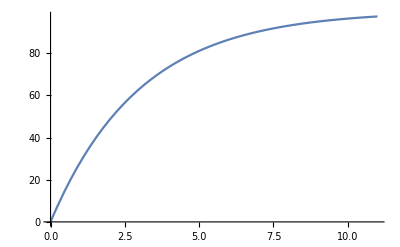

```mathematica
Plot[μ[t],{t,0,11}]
```

```mathematica
μ[100]//N
```

100.

```mathematica
t0=Table[i,{i,0,nintervals}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
μ[0]
```

0

```mathematica
ListPlot[Table[U[N0,x],{x,0,1,0.1}]]
```

-Graphics-

```mathematica
Plot[U[x,b0],{x,1,200}]
```

-Graphics-

```mathematica
U[n_,b_]=Simplify[N[Sum[-PowerExpand[Log[Simplify[PDF[PoissonDistribution[μ1[i,n,b]-μ1[i-1,n,b]],x],x>0]]]/.x->data[[i]],{i,1,nintervals}]],n>0&&b>0](*+If[Total[data]<N0,CDF[PoissonDistribution[N0-Total[data]]],0]*)
```

158.219+288. b+1. n-1. ⅇ^(-10. b) n-90. Log[-1.+1. ⅇ^(1. b)]-90. Log[n]

```mathematica
dU[x_,y_]=Simplify[N[GradientG[U[x,y],{x,y}]],x>0&&y>0]
```

{1.-1. ⅇ^(-10. y)-90./x,288.-(90. ⅇ^(1. y))/(-1.+1. ⅇ^(1. y))+10. ⅇ^(-10. y) x}

```mathematica
ddU[x_,y_]=N[HessianH[U[x,y],{x,y}]]
```

{{90./x^2,10. 2.71828^(-10. y)},{10. 2.71828^(-10. y),(90. 2.71828^(2. y))/((-1.+1. 2.71828^(1. y))^2)-(90. 2.71828^(1. y))/(-1.+1. 2.71828^(1. y))-100. 2.71828^(-10. y) x}}

```mathematica
INTERVAL=1001;
STEPS=3;
CHAINS=3;
dt10=0.0000000001;
dt20=0.0000000001;
Dim=2;
qinit=RandomReal[UniformDistribution[],{CHAINS,Dim}];
outbnd[q_]:=AnyTrue[q,(#<0)&];
```

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True,qinit];
```

10011.0161×10^80.6332250.5185730.50082760.12831.0161×10^84.66892×10^85.7565×10^-60.000026451True{1}{4}

20025.13581×10^8161.0760.06655290.067858661.36881.11771×10^85.13581×10^86.33215×10^-60.0000352063False{1,2}{4}

30038.39748×10^72.283160.6711030.39661759.23588.39749×10^71.98008×10^85.7565×10^-60.00006237True{1,2,4}{1,4}

40041.22947×10^8120.8240.5821020.51539460.52361.98008×10^81.22947×10^84.32495×10^-60.00006237False{1,3}{1,4}

50059.23723×10^71.814020.8131740.28923764.61849.23724×10^73.91748×10^73.93177×10^-60.000110492True{1,3}{1,4}

60063.91748×10^7201.4330.6816880.55133263.25159.23724×10^73.91748×10^73.93177×10^-60.000110492False{1,3}{1,4}

70079.23723×10^71.274320.8423690.18750761.57569.23724×10^73.91748×10^73.93177×10^-60.000110492True{1,3}{1,4}

80083.91748×10^7337.0380.3720610.54562259.93319.23724×10^73.91748×10^73.93177×10^-60.000110492False{1,3}{1,4}

90099.23723×10^74.866251.0.60.22459.23724×10^73.91748×10^73.93177×10^-60.000110492True{1,3}{1,4}

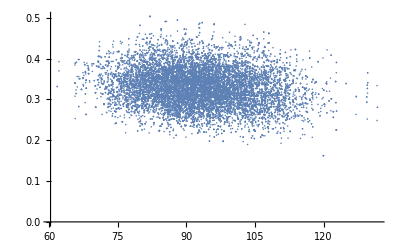

```mathematica
ListPlot[QS]
```